# IP3R

## Example

```mathematica
c1=0.185;
```

```mathematica
volCytInL=10^-14;
volErInL=c1*volCytInL;
volTotalInL=volCytInL+volErInL;
```

```mathematica
volErinM3=0.001*volErInL;
```

```mathematica
(* Assume ER = sphere = min surface area *)
radiusErInM=(volErinM3/(4*Pi/3))^(1/3)
```

7.61543×10^-7

```mathematica
surfaceAreaErInM2=4*Pi*radiusErInM^2
```

7.28784×10^-12

```mathematica
(* The Er probably is not a sphere; has some folds.... Some fudge factor here *)
surfaceAreaErInM2*=10;
```

```mathematica
surfaceAreaErInuM2=surfaceAreaErInM2*10^12
```

72.8784

```mathematica
(* Assume its a grid *)
sideLengthErinuM=Sqrt[surfaceAreaErInuM2]
```

8.53688

```mathematica
(* Spacing of IP3R clusters is 1-7 uM => 5uM *)
spacingIP3RClusterinuM=5;
noIP3RClusterperSide=sideLengthErinuM/spacingIP3RClusterinuM
```

1.70738

```mathematica
noIP3RCluster=noIP3RClusterperSide^2
```

2.91513

```mathematica
(* BUT! This is a cluster; each cluster contains up to 15 channels *)
noIP3RChannels=noIP3RCluster*10
```

29.1513

```mathematica
(* Each channel contains 3/4 subunits *)
noIP3RSubunits=4*noIP3RChannels
```

116.605

## Plot

```mathematica
noSubunits[surfAreaFactor_,spacingIP3RClusterinuM_,volExp_]:=Module[
{surfaceAreaErInM2work,surfaceAreaErInuM2,sideLengthErinuM,noIP3RClusterperSide,noIP3RCluster,noIP3RChannels,noIP3RSubunits,c1,volCytInL,volStr,volErInL,volTotalInL,volErinM3,radiusErInM,surfaceAreaErInM2}
,
c1=0.185;

volCytInL=10^-volExp;
volErInL=c1*volCytInL;
volTotalInL=volCytInL+volErInL;
volErinM3=0.001*volErInL;

(* Assume ER = sphere = min surface area *)
radiusErInM=(volErinM3/(4*Pi/3))^(1/3);
surfaceAreaErInM2=4*Pi*radiusErInM^2;

(* The Er probably is not a sphere; has some folds.... Some fudge factor here *)
surfaceAreaErInM2work=surfaceAreaErInM2*surfAreaFactor;

surfaceAreaErInuM2=surfaceAreaErInM2work*10^12;

(* Assume its a grid *)
sideLengthErinuM=Sqrt[surfaceAreaErInuM2];

(* Spacing of IP3R clusters is 1-7 uM => 5uM *)
noIP3RClusterperSide=sideLengthErinuM/spacingIP3RClusterinuM;
noIP3RCluster=noIP3RClusterperSide^2;

(* BUT! This is a cluster; each cluster contains up to 15 channels *)
noIP3RChannels=noIP3RCluster*10;

(* Each channel contains 3/4 subunits *)
noIP3RSubunits=4*noIP3RChannels;

Return[noIP3RSubunits]
];
```

```mathematica
spacings=Table[spacingIP3RClusterinuM,{spacingIP3RClusterinuM,2,7}];
spacingLabels=Table["Δx_(IP3R clusters) = "<>ToString[s]<>" μm",{s,spacings}];
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
leg=LineLegend[colors[[;;Length[spacings]]],spacingLabels]
```

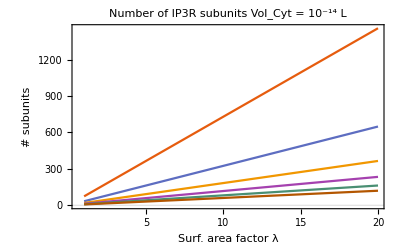
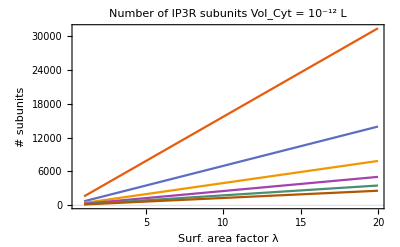
-Graphics- | -Graphics- |

```mathematica
plt=Grid[{{
ListLinePlot[
Table[
Table[
noSubunits[surfAreaFactor,spacingIP3RClusterinuM,14]
,{surfAreaFactor,1,20}]
,{spacingIP3RClusterinuM,spacings}],
PlotRange->All,
FrameLabel->{"Surf. area factor λ","# subunits"},
PlotLabel->"Number of IP3R subunits \n Vol_Cyt = 10^-14 L"
],
ListLinePlot[
Table[
Table[
noSubunits[surfAreaFactor,spacingIP3RClusterinuM,12]
,{surfAreaFactor,1,20}]
,{spacingIP3RClusterinuM,spacings}],
PlotRange->All,
FrameLabel->{"Surf. area factor λ","# subunits"},
PlotLabel->"Number of IP3R subunits \n Vol_Cyt = 10^-12 L"
],
leg
}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["no_ip3r_subunits.pdf",plt]
Export["no_ip3r_subunits.png",plt,ImageResolution->200]
```

no_ip3r_subunits.pdf

no_ip3r_subunits.png

```mathematica
plt3d=Plot3D[
noSubunits[surfAreaFactor,spacingIP3RClusterinuM,12],{surfAreaFactor,1,10},{spacingIP3RClusterinuM,2,7},
PlotRange->All,
AxesLabel->{"Surf. area factor λ","Δx_IP3 (μm)"},
PlotLabel->"# IP3R subunits for Vol: "<>volStr<>" L",
BaseStyle->Directive[FontSize->24],
ImageSize->500
]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["vol_exp_"<>ToString[volExp]<>".pdf",plt3d]
Export["vol_exp_"<>ToString[volExp]<>".png",plt3d,ImageResolution->200]
```

vol_exp_14.pdf

vol_exp_14.png

## Plot by surf area factor

```mathematica
surfAreaFactors=Table[i,{i,1,13,3}];
surfAreaLabels=Table["λ = "<>ToString[s],{s,surfAreaFactors}];
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
leg=LineLegend[colors[[;;Length[surfAreaFactors]]],surfAreaLabels]
```

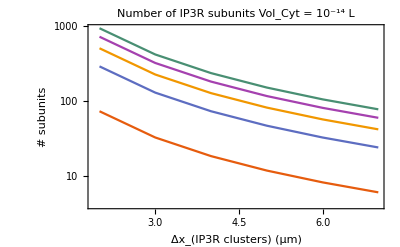
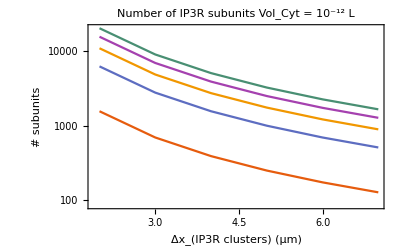
-Graphics- | -Graphics- |

```mathematica
plt=Grid[{{
ListLogPlot[
Table[
Table[
{spacingIP3RClusterinuM,noSubunits[surfAreaFactor,spacingIP3RClusterinuM,14]}
,{spacingIP3RClusterinuM,spacings}]
,{surfAreaFactor,surfAreaFactors}],
PlotRange->All,
FrameLabel->{"Δx_(IP3R clusters) (μm)","# subunits"},
PlotLabel->"Number of IP3R subunits \n Vol_Cyt = 10^-14 L"
]/.Point->Line,
ListLogPlot[
Table[
Table[
{spacingIP3RClusterinuM,noSubunits[surfAreaFactor,spacingIP3RClusterinuM,12]}
,{spacingIP3RClusterinuM,spacings}]
,{surfAreaFactor,surfAreaFactors}],
PlotRange->All,
FrameLabel->{"Δx_(IP3R clusters) (μm)","# subunits"},
PlotLabel->"Number of IP3R subunits \n Vol_Cyt = 10^-12 L"
]/.Point->Line,
leg
}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["no_ip3r_subunits_by_spacing.pdf",plt]
Export["no_ip3r_subunits_by_spacing.png",plt,ImageResolution->200]
```

no_ip3r_subunits_by_spacing.pdf

no_ip3r_subunits_by_spacing.png

# Serca

```mathematica
(* SERCA pump density *)
sercaDensityPeruM2=1000;
noSerca=surfaceAreaErInuM2*sercaDensityPeruM2
```

72878.4

```mathematica
(* Alternate SERCA *)
sercaDensityinuM=15; (* 15-75 as per Higgins paper *)
sercaDensityinM=10^-6*sercaDensityinuM;
avogadro=6.02214076*10^23;
noSerca=sercaDensityinM*avogadro*volCytInL
```

90332.1